```mathematica
Nm=12;
μ0=-2.0;
ϵ=-1;
```

```mathematica
A[ϕ_]:= 2ϕ-1;
B[J_]:= Exp[-J];
```

```mathematica
μ[ϕ_,J_]:=2 Log[A[ϕ] √B[J]+√(1 + A[ϕ]^2(B[J]-1))]-Log[1-A[ϕ]^2]-J;
```

```mathematica
μr[ϕ_,nt_]:= μ0 + Log[nt - Nm ϕ + 1];
```

```mathematica
dμr[ϕ_,nt_]:= -Nm/(nt-Nm ϕ + 1);
```

```mathematica
FindRoot[μ[ϕ,1] - μr[ϕ,10]==dμr[ϕ,10]ϕ-ϵ,{ϕ,0.7}]
```

{ϕ→0.538053}

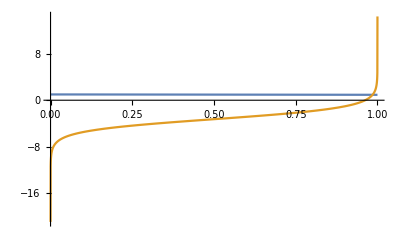

```mathematica
Plot[{dμr[ϕ,200]ϕ-ϵ, μ[ϕ,0]-μr[ϕ,200]},{ϕ,0,1}, PlotRange->Full]
```

```mathematica
X[J_,μ_]:= 1/2(J+μ);
```

```mathematica
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√(Sinh[X[J,μ]]^2+B[J]));
vm[J_,μ_]:= Exp[-μ/2](λm[J,μ]-1);
```

```mathematica
ϕnd[J_,μ_]:= 1/(1+vm[J,μ]^2);
```

```mathematica
μt[nt_] := μ0 + Log[nt]-ϵ;
```

```mathematica
N[ϕnd[0,μt[200]]]
```

0.857944